```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/WC/WC_COND_RESULTS/"];
filePerf={"bulk/PERF/t_kappa31.dat","100/PERF/t_kappa31.dat","10/PERF/t_kappa31.dat","1/PERF/t_kappa31.dat","0.1/PERF/t_kappa31.dat"};
fileIso={"bulk/ISO/t_kappa31.dat", "100/ISO/t_kappa31.dat" ,"10/ISO/t_kappa31.dat","1/ISO/t_kappa31.dat","0.1/ISO/t_kappa31.dat"};
fileExp={"sam.exp.1900Ksample.WC.conductivity"};
fileBoltz={"RESULTS_output_WC_electronic_conductivity/hte.trace"};
wcCondPerf=Table[ReadList[filePerf[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,filePerf//Length}];
wcCondIso=Table[ReadList[fileIso[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,fileIso//Length}];
wcCondExp=Table[ReadList[fileExp[[i]],{Number, Number}],{i,1,fileExp//Length}];
wcCondBoltz=Table[ReadList[fileBoltz[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number,Number}],{i,1,fileExp//Length}];
(*"0.1bmf/PERF/t_kappa31.dat", "0.1bmf/ISO/t_kappa31.dat"*)
```

```mathematica
condWCperf=Table[Transpose[{Transpose[wcCondPerf[[i]]][[1]],Transpose[wcCondPerf[[i]]][[2]]}],{i,1,5,1}];
condWCiso=Table[Transpose[{Transpose[wcCondIso[[i]]][[1]],Transpose[wcCondIso[[i]]][[2]]}],{i,1,5,1}];
```

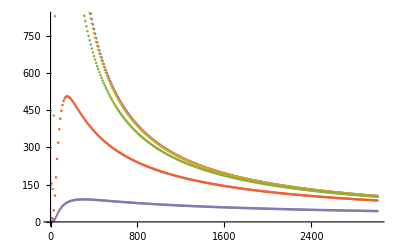

```mathematica
ListPlot[condWCperf]
```

```mathematica
optionsWC={AspectRatio->1.4,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLegends->Placed[SwatchLegend[{Style["κ_ph[100000 μm]",15],Style["κ_ph[100 μm]",15],Style["κ_ph[10 μm]",15],Style["κ_ph1 μm]",15],Style["κ_ph[0.1 μm]",15]}],{0.80,0.70}],PlotLabel->Style["WC thermal conductivity",15],PlotStyle->Thickness[0.007],PlotRange->{{0,3000},{0,500}}};
options2WC={AspectRatio->1.4,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["WC thermal conductivity",15],PlotStyle->Thickness[0.007],PlotRange->{{0,3000},{0,500}}};
```

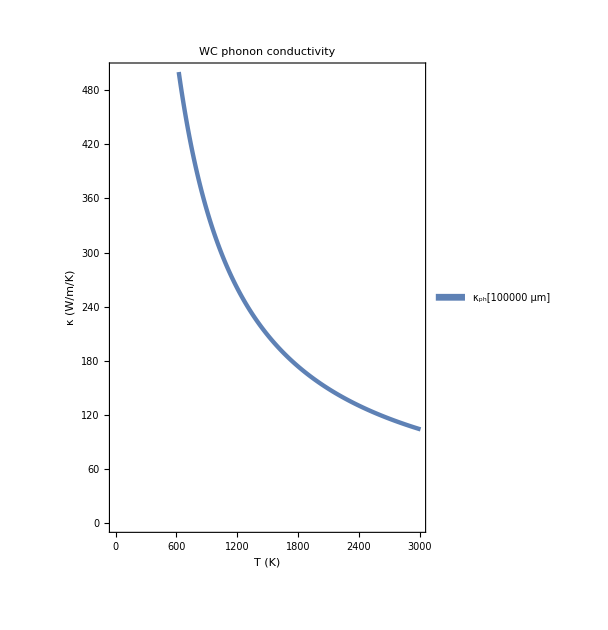

```mathematica
Show[{ListLinePlot[condWCperf[[1;;1]],Evaluate[optionsWC]]}]
```

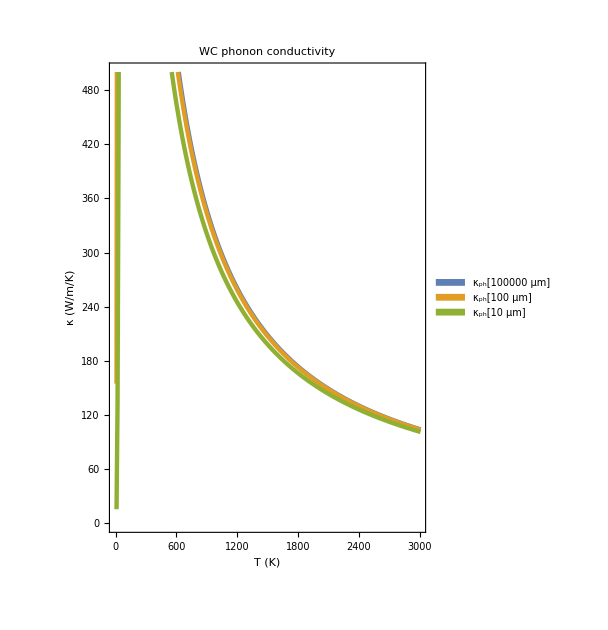

```mathematica
Show[{ListLinePlot[condWCperf[[1;;3]],Evaluate[optionsWC]]}]
```

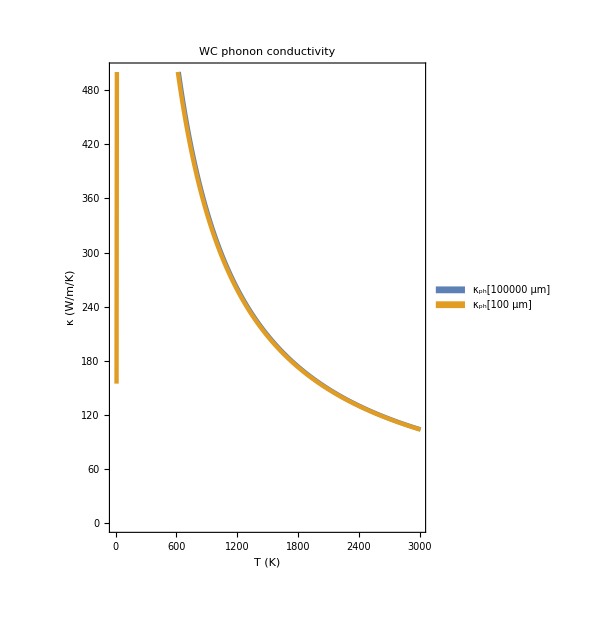

```mathematica
Show[{ListLinePlot[condWCperf[[1;;2]],Evaluate[optionsWC]]}]
```

```mathematica
Show[{ListLinePlot[condWCperf[[1;;3]],Evaluate[optionsWC]]}]
```

-Graphics-

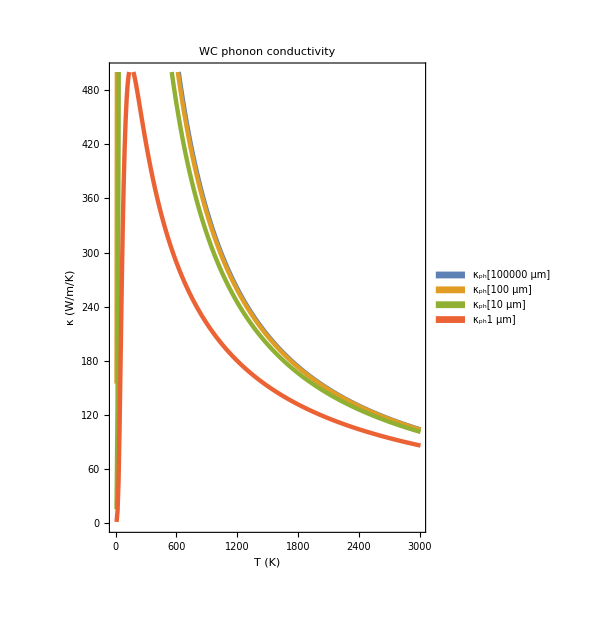

```mathematica
Show[{ListLinePlot[condWCperf[[1;;4]],Evaluate[optionsWC]]}]
```

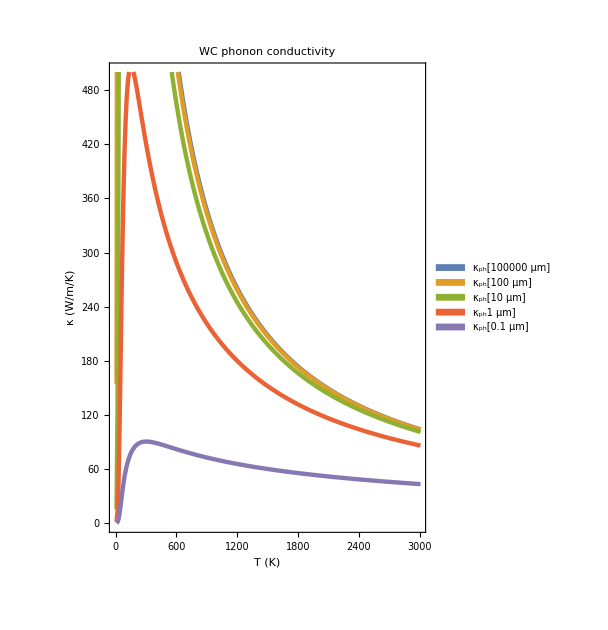

```mathematica
Show[{ListLinePlot[condWCperf[[1;;5]],Evaluate[optionsWC]]}]
```

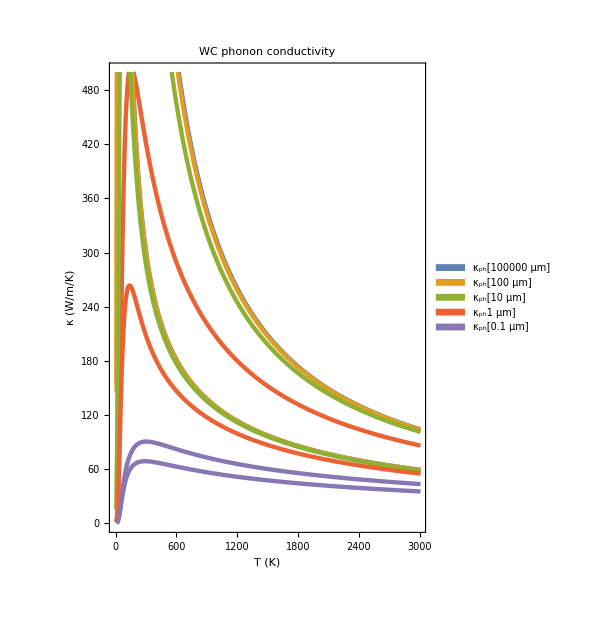

```mathematica
Show[{ListLinePlot[condWCperf,Evaluate[optionsWC]],ListLinePlot[condWCiso,Evaluate[options2WC]]}]
```

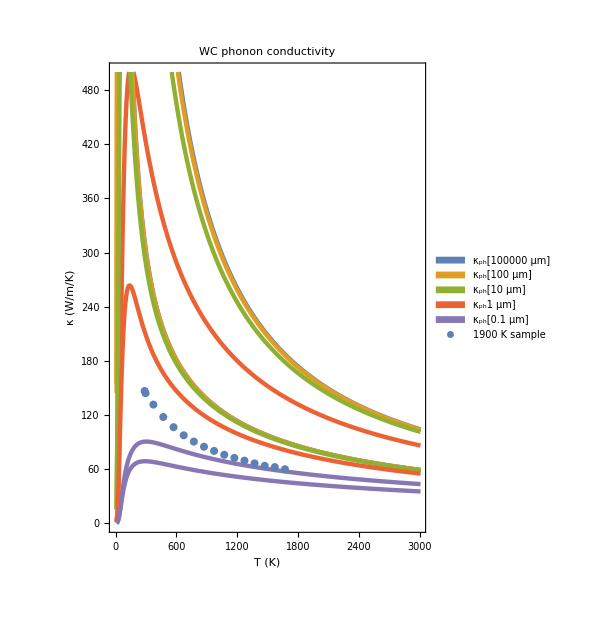

```mathematica
Show[{ListLinePlot[condWCperf,Evaluate[optionsWC]],ListLinePlot[condWCiso,Evaluate[options2WC]],ListPlot[wcCondExp,PlotLegends->{"1900 K sample"}]}]
```

```mathematica
wcCondBoltz[[1]][[2]]
```

{-0.00008,60.,0.0139927,226.816,-9.10971×10^-7,2.26803×10^20,1.04445×10^-9,3.39312×10^14,1.1901,3.38618×10^-9}

220

InterpolatingFunction[{{30., 3300.}}, <>]

-Graphics-

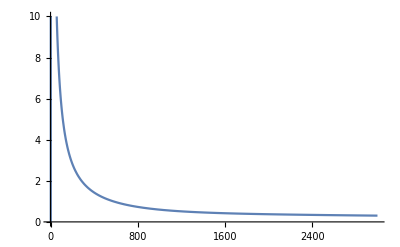

```mathematica
condel=Transpose@{Transpose[wcCondBoltz[[1]]][[2]][[1;;110]],Transpose[wcCondBoltz[[1]]][[8]][[1;;110]]};
Intercondel=Interpolation[condel]
ListPlot[condel]
Plot[10^-10*Intercondel[x]/x^2,{x,1,3000},PlotRange->{{0,3000},{0,10}}]
```

```mathematica
IntercondWCperf=Table[Interpolation@Transpose[{Transpose[wcCondPerf[[i]]][[1]],Transpose[wcCondPerf[[i]]][[2]]}],{i,1,5,1}];
IntercondWCiso=Table[Interpolation@Transpose[{Transpose[wcCondIso[[i]]][[1]],Transpose[wcCondIso[[i]]][[2]]}],{i,1,5,1}];
```

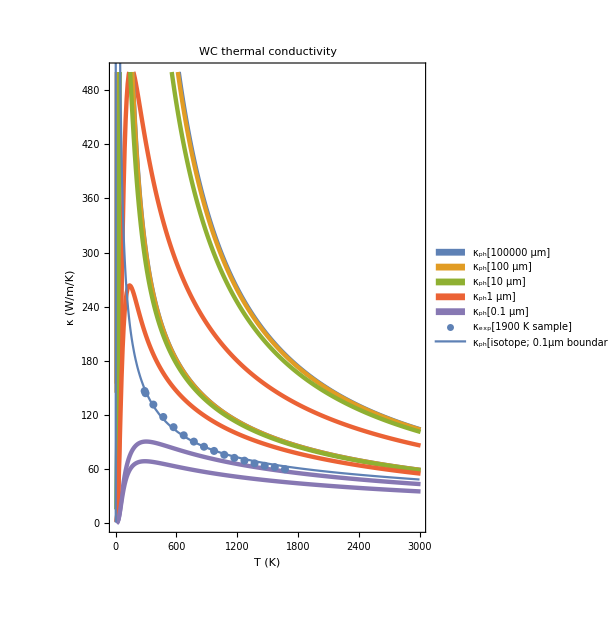

```mathematica
With[{a=40,b=-1},Show[{ListLinePlot[condWCperf,Evaluate[optionsWC]],ListLinePlot[condWCiso,Evaluate[options2WC]],ListPlot[wcCondExp,PlotLegends->{"κ_exp[1900 K sample]"}],Plot[IntercondWCiso[[5]][x]+a*10^-10Intercondel[x]/x^2-b,{x,1,3000},PlotRange->{{1,3000},{1,1000}},PlotLegends->{" κ_ph[isotope; 0.1μm boundary] + κ_el[fitted τ_(el - ph)=A/T^2]"}]}]]
```

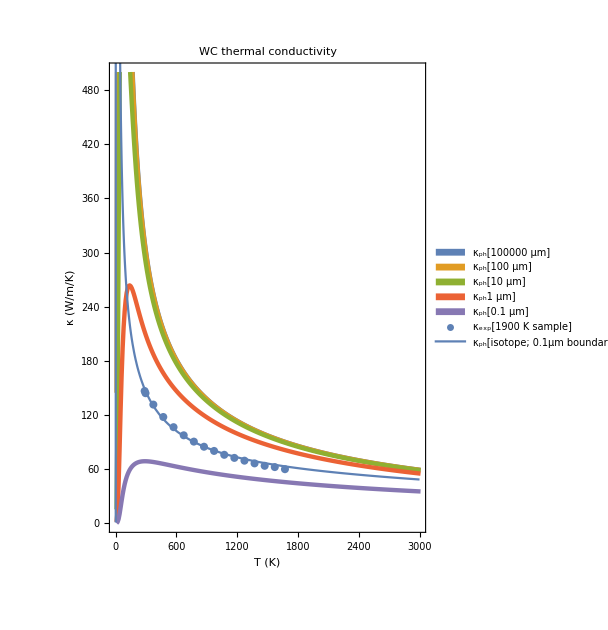

```mathematica
With[{a=40,b=-1},Show[{ListLinePlot[condWCiso,Evaluate[optionsWC]],ListPlot[wcCondExp,PlotLegends->{"κ_exp[1900 K sample]"}],Plot[IntercondWCiso[[5]][x]+a*10^-10Intercondel[x]/x^2-b,{x,1,3000},PlotRange->{{1,3000},{1,1000}},PlotLegends->{" κ_ph[isotope; 0.1μm boundary] + κ_el[fitted τ_(el - ph)=A/T^2]"}]}]]
```